```mathematica
Orysya Stus
A10743411
```

# Homework 2

Please email the Mathematica notebook and a pdf of the notebook output to beng123@gmail.com with the subject line HOMEWORK 2 - YOUR NAME - YOUR PID. This homework is due at the start of class on Thursday (3:30 pm). Everything you need to know for Mathematica is in the corresponding notebook files. Remember that explanations should accompany the plots for each of the questions. Also, please suppress the Mathematica code input by double left-clicking on all the output brackets.

Note: This homework requires the use of the file GraphicsDirective.m (available on the assignments page of the course website). In order for graphics to show correctly it has to be in the same folder as this notebook. There is no need to email us the GraphicsDirective.m file when submitting this homework. Import the file by running the following code:

```mathematica
SetDirectory[NotebookDirectory[]];
<<"GraphicsDirectives.m"
```

It might also be beneficial for you to clear all variables between problems. Do this by adding in this line of code before starting each problem (You will have to reimport GraphicsDirective)

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"GraphicsDirectives.m"
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

## Problem 1

Do Problem 3.2 from the textbook.

### Put your solution here:

```mathematica
P= MatrixForm[{{1,1,0},{2,1,0}, {1,1,1}, {3,2,1}}]
```

(1 | 1 | 0
2 | 1 | 0
1 | 1 | 1
3 | 2 | 1)

## Problem 2

Do Problem 3.3 from the textbook without using MASSToolbox by defining the differential equations and solving. Steps have been put in place to assist you. Enter your solutions in the space provided beneath each step. Skip the the second bullet (“Compute the correlation...”).

### Run this first:

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"GraphicsDirectives.m"
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

### Step 1: Define the stoichiometric matrix and differential equations

Hint: For example, use (rhs1
.
.)=(1 | . | .
1 | . | .
. | . | .).(v1
.
.)

```mathematica
({{rhs1}, {rhs2}, {rhs3}, {rhs4}})=({{-1, 0, 0}, {1, -1, 0}, {0, 1, -1}, {0, 0, 1}}).({{v1}, {v2}, {v3}});
```

### Step 2: Define rate laws and parameter values

```mathematica
v1=k1*(x1[t] - x2[t]/K1);
v2 =k2 *(x2[t] - x3[t]/K2);
v3 = k3*x3[t];
```

```mathematica
k1=1.0; k2 = 0.01 ; k3 = 0.0001;
K1 = K2 = 2;
```

### Step 3: Set up the conditions and solve

Hint: Use the Mathematica help documentation to find out more about NDSolve

```mathematica
?NDSolve
```

```mathematica
tfinal = 50000;
```

```mathematica
solution= 
NDSolve[{x1'[t]==rhs1, x2'[t]==rhs2, x3'[t]==rhs3,x4'[t]==rhs4, x1[0]==1.0,x2[0]==0, x3[0]==0, x4[0]==0.},{x1,x2,x3,x4},{t,0,tfinal}][[1]];
```

```mathematica
X[t_]:=({{x1[t]/.solution}, {x2[t]/.solution}, {x3[t]/.solution}, {x4[t]/.solution}});
```

### Step 4: Plot

Hint: Use LogLinearPlot

```mathematica
?LogLinearPlot
```

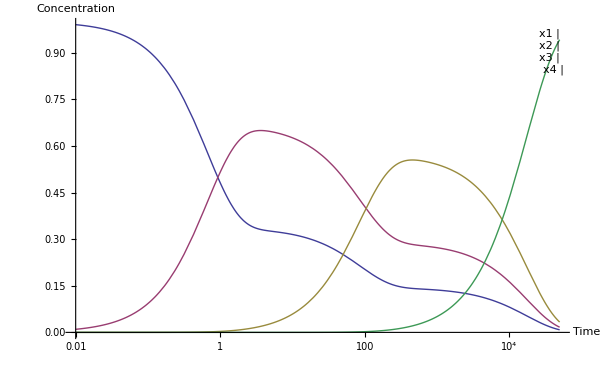

```mathematica
Quiet@LogLinearPlot[Evaluate[X[t]],{t,0.01,tfinal},AxesLabel->{"Time","Concentration"},Epilog->createLegend[{"x1","x2","x3","x4"}]]
```

```mathematica
The reversible processes all approach 0 while the irreversible process (the formation of x4) is favored thus the concentration of x4 increases.
```

### Step 5: Define pool forming matrix

```mathematica
P= ({{1, -0.5, 0, 0}, {1, 1, -0.75, 0}, {1, 1, 1, 0}});
```

### Step 6: Plot pool phase portraits

Hint: Search Mathematica help documentation for usage of ParametricPlot

```mathematica
pools = P.Flatten[X[t]];
```

```mathematica
poolLabels={pool1,pool2,pool3};
```

```mathematica
plts=Table[If[i>j,ParametricPlot[pools[[{j,i}]],{t,0,tfinal},ImageSize->250,LabelStyle->{FontSize->12},PlotPoints->10000,Epilog->ppAnnotate[pools[[{j,i}]][[All,0]],solution,tfinal],FrameLabel->poolLabels[[{j,i}]]],If[i==j,Quiet@LogLinearPlot[pools[[i]],{t,1*^-4,tfinal},ImageSize->250,Axes->False,LabelStyle->{FontSize->12},FrameLabel->{"t","conc"},Frame->True,Epilog->Inset@Text[poolLabels[[i]]]]]],{i,1,Length[poolLabels]},{j,1,Length[poolLabels]}];
```

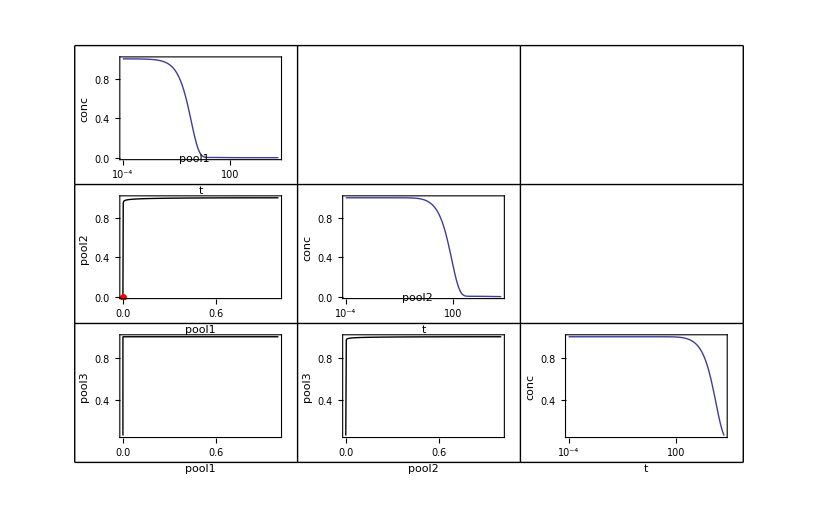

```mathematica
GraphicsGrid[plts, Frame->All]
```

```mathematica
The pool formation matrix did generate dynamically independent pools as demonstrated by the graphs of pool2 vs. pool1, pool3 vs. pool1, and pool3 vs. pool2 where the graph takes an L shape.
```

## Problem 3

Do problem 3.5 from the textbook without using MASSToolbox.

### Put your solution here:

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<"GraphicsDirectives.m"
```

General::obspkg: "PlotLegends`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
({{rhs1}, {rhs2}, {rhs3}, {rhs4}, {rhs5}})=({{-1, 0, 0, 0}, {1, -1, 0, 0}, {0, 1, -1, 0}, {0, 0, 1, -1}, {0, 0, 0, 1}}).({{v1}, {v2}, {v3}, {v4}});
```

```mathematica
v1=k1*(x1[t] - x2[t]/K1);
v2 =k2 *(x2[t] - x3[t]/K2);
v3 =k3*(x3[t] -x4[t]/K3);
v4 = k4*x4[t];
```

```mathematica
k1=1.0; k2 = 0.01 ; k3 = 0.0001; k4=0.000001;
K1 = K2 = K3=1;
```

```mathematica
tfinal = 50000000;
```

```mathematica
solution= 
NDSolve[{x1'[t]==rhs1, x2'[t]==rhs2, x3'[t]==rhs3,x4'[t]==rhs4, x5'[t]==rhs5, x1[0]==1.0,x2[0]==0, x3[0]==0, x4[0]==0, x5[0]==0.},{x1,x2,x3,x4,x5},{t,0,tfinal}][[1]];
```

```mathematica
X[t_]:=({{x1[t]/.solution}, {x2[t]/.solution}, {x3[t]/.solution}, {x4[t]/.solution}, {x5[t]/.solution}});
```

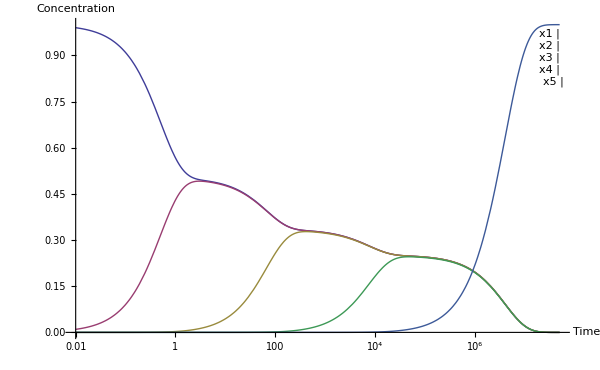

```mathematica
Quiet@LogLinearPlot[Evaluate[X[t]],{t,0.01,tfinal},AxesLabel->{"Time","Concentration"},Epilog->createLegend[{"x1","x2","x3","x4", "x5"}]]
```

```mathematica
Similar to the graph in Prob 2, the reversible processes (x1-x4) all have their concentrations approaching 0 while the formation of the irreversible process allows the concentration of x5 to increase.
```

```mathematica
P = ({{1, -1, 0, 0, 0}, {1, 1, -2, 0, 0}, {1, 1, 1, -3, 0}, {1, 1, 1, 1, 0}});
```

```mathematica
pools = P.Flatten[X[t]];
```

```mathematica
poolLabels={pool1,pool2, pool3,pool4};
```

```mathematica
plts=Table[If[i>j,ParametricPlot[pools[[{j,i}]],{t,0,tfinal},ImageSize->250,LabelStyle->{FontSize->12},PlotPoints->10000,Epilog->ppAnnotate[pools[[{j,i}]][[All,0]],solution,tfinal],FrameLabel->poolLabels[[{j,i}]]],If[i==j,Quiet@LogLinearPlot[pools[[i]],{t,1*^-4,tfinal},ImageSize->250,Axes->False,LabelStyle->{FontSize->12},FrameLabel->{"t","conc"},Frame->True,Epilog->Inset@Text[poolLabels[[i]]]]]],{i,1,Length[poolLabels]},{j,1,Length[poolLabels]}];
```

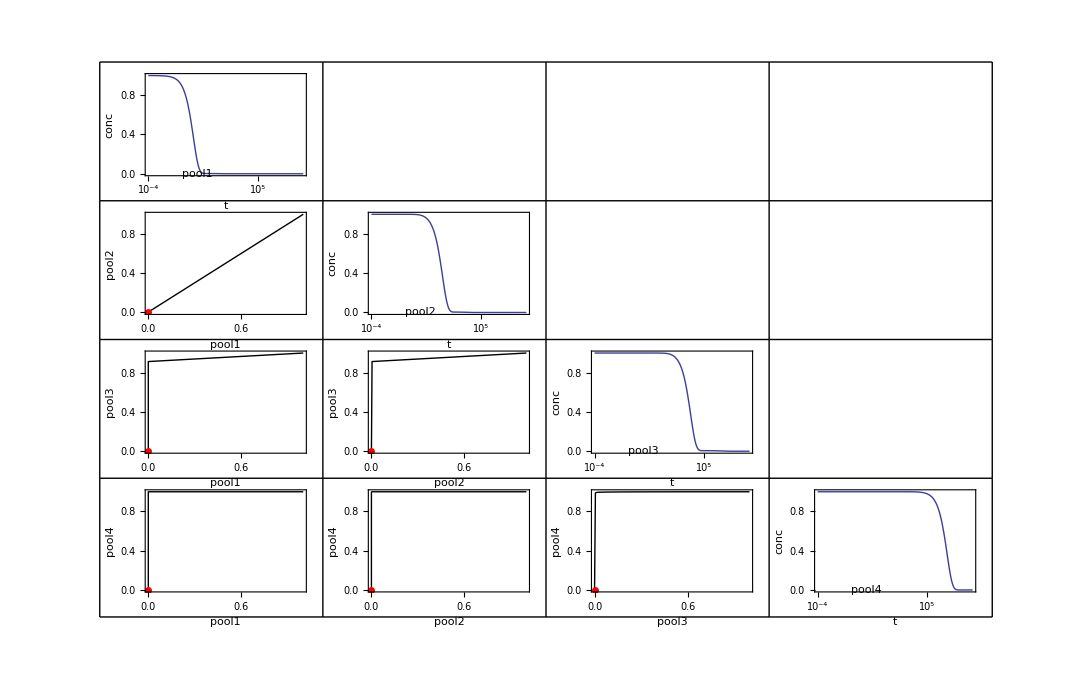

```mathematica
GraphicsGrid[plts, Frame->All]
```

```mathematica
Yes, you can generalize this result to 5,6,7,...n reversible reactions in a series where all the equilibrium constants are unity as provided by the results of Prob 1 and Prob 2 where each variable is independent of one another. And any additional reversible linear reactions will become additional rows in the original matrix S in the expresion of rhs following a pattern as shown above. 

If the reactions are irreversible(K->infinity), then the original matrix will only be a diagonal of 1's, the graph of concentration vs. time will show the prevalence of x5 increasing, and the results of the pools would be dependent on another.
```

## Problem 4

Do problem 4.1 from the textbook using MASSToolbox. Make use the manipulate function in order to vary the value of k2

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<Toolbox`
<<Toolbox`Style`
```

Legend::shdw: Symbol "Legend" appears in multiple contexts {"Toolbox`", "PlotLegends`"}; definitions in context "Toolbox`" may shadow or be shadowed by other definitions.

### Put your solution here:

```mathematica
tfinal=1000;
Manipulate[plotSimulation[simulate[constructModel[str2mass /@ {
      "1: x1 <=> x2",
      "2: x2 --> x3",
      "3: x3 <=> x4"},
    InitialConditions -> {
      metabolite["x1", None] -> 1,
      metabolite["x2", None] -> 0,
      metabolite["x3", None] -> 0,
      metabolite["x4", None] -> 0},
    Parameters -> {rateconst["1", True] -> 1,
      rateconst["2", True] -> a,
      rateconst["3", True] -> 1,
      Keq["1"] -> 1,
      Keq["3"] -> 1}],
   {t, 0, tfinal}][[1]], {t, 0, tfinal},
 PlotFunction -> LogLinearPlot, PlotLegends -> {Position->{Left,Bottom}}], {a, {1, 0.1, 0.01}}]
```

```mathematica
As k2 -> 0 (or low values), the dynamics of the system favors the formation of x4 with the levels of x1 and x2 decreasing to 0.
```

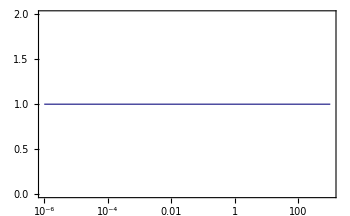

```mathematica
model=constructModel[str2mass /@ {"1: x1 <=> x2","2: x2 --> x3","3: x3 <=> x4"},
    InitialConditions -> {
      metabolite["x1", None] -> 1,
      metabolite["x2", None] -> 0,
      metabolite["x3", None] -> 0,
      metabolite["x4", None] -> 0},
    Parameters -> {rateconst["1", True] -> 1,
      rateconst["2", True] -> 1,
      rateconst["3", True] -> 1,
      Keq["1"] -> 1,
      Keq["3"] -> 1}];

{concProfile, fluxProfile} = simulate[model, {t,0,1000}];
pools = {"p1" -> metabolite["x1",None] + metabolite["x2", None] + metabolite["x3", None] + metabolite["x4", None]};

plotSimulation[pools/.concProfile,PlotFunction ->LogLinearPlot]
```

```mathematica
Therefore p2 + p4 = p1 is a constant.


tfinal=1000;
```

```mathematica
Manipulate[plotSimulation[simulate[constructModel[str2mass /@ {
      "1: x1 <=> x2",
      "2: x2 --> x3",
      "3: x3 <=> x4"},
    InitialConditions -> {
      metabolite["x1", None] -> 1,
      metabolite["x2", None] -> 0,
      metabolite["x3", None] -> 0,
      metabolite["x4", None] -> 0},
    Parameters -> {rateconst["1", True] -> 1,
      rateconst["2", True] -> 1,
      rateconst["3", True] -> b,
      Keq["1"] -> 1,
      Keq["3"] -> 1}],
   {t, 0, tfinal}][[1]], {t, 0, tfinal},
 PlotFunction -> LogLinearPlot, PlotLegends -> {Position->{Left,Bottom}}], {b, {0.01, 1, 100}}]
```

```mathematica
The dynamics of the reaction do not change because the production of x4 remains in favor.
```

## Problem 5

Do problem 4.5 from the textbook.

#### Put your solution here:

```mathematica
matrixS = ({{-1, 1, 0, 0, 0}, {1, -1, -1, 0, 0}, {0, 0, 1, -1, 1}, {0, 0, 0, 1, -1}});
matrixS'= ({{-1, 0, 0}, {1, -1, 0}, {0, 1, 1}, {0, 0, -1}});
```

```mathematica
vectorV' = ({{Subscript[k, 1] Subscript[x, 1]}, {Subscript[k, 2] Subscript[x, 2]}, {Subscript[k, 3] Subscript[x, 3]}});
leftnullspaceofS = NullSpace[Transpose[matrixS]]
```

{{1,1,1,1}}

```mathematica
leftnullspaceofS' = NullSpace[Transpose[matrixS']]
```

{{1,1,1,1}}

```mathematica
leftnullspaceofS = leftnullspaceofS'
```

{{1,1,1,1}}

```mathematica
Therefore the left null space does not change. The left null space does not change if the reactions are irreversible.
```